```mathematica
N@Zeta[1000I-.5]
```

-123.541+90.0001 ⅈ

```mathematica
N@Zeta[1000I+.5]
```

0.356334+0.931998 ⅈ

```mathematica
0.3563343671948756
```

```mathematica
N@Zeta[1000I-1]
```

-1575.36018680522+1109.53796564106 ⅈ

```mathematica
N@Zeta[1000I+2]
```

0.953262-0.110723 ⅈ

```mathematica
N@Zeta[1000I-1/4]
```

-33.6146902075769+26.7555297431193 ⅈ

```mathematica
N@ZetaZero[10000]
```

```mathematica
0.5+9877.782654005501 ⅈ
```

```mathematica
0.5
+14.134725141734695 ⅈ
```

```mathematica
0.5+49.7738324776723 ⅈ
```

```mathematica
0.5+
236.5242296658162 ⅈ
```

```mathematica
0.5+1419.4224809459956 ⅈ
```

```mathematica
N[Zeta[1+1000I]]
```

```mathematica
0.9409368682928779+0.045226652072133965 ⅈ
```

```mathematica
x^(A+f I)/(A+f I)/.x->100./.A->-.5/.f->Im@ZetaZero@1
```

0.00560796+0.00430588 ⅈ

```mathematica
x^A E^(Log[x]f I)/(A+f I)/.x->100./.A->-.5/.f->Im@ZetaZero@1
```

0.00560796+0.00430588 ⅈ

```mathematica
(A-f I)x^A E^(Log[x]f I)/(A^2+f^2)/.x->100./.A->-.5/.f->Im@ZetaZero@1
```

0.00560796+0.00430588 ⅈ

```mathematica
(x^A/(A^2+f^2)) (A-f I)(Cos[f Log[x]] + I Sin[f Log[x]]) /.x->100./.A->-.5/.f->Im@ZetaZero@1
```

0.00560796+0.00430588 ⅈ

```mathematica
(x^A/(A^2+f^2)) (A Cos[f Log[x]]-f I Cos[f Log[x]] + I A Sin[f Log[x]]+f Sin[f Log[x]]) /.x->100./.A->-.5/.f->Im@ZetaZero@1
```

0.00560796+0.00430588 ⅈ

```mathematica
Expand[(A+f I)(A-f I)]
```

A^2+f^2

```mathematica
(x^A/(A^2+f^2)) (A Cos[f Log[x]]+f Sin[f Log[x]]+I( A Sin[f Log[x]]-f Cos[f Log[x]])) /.x->100./.A->-.5/.f->Im@ZetaZero@1
```

0.00560796+0.00430588 ⅈ

```mathematica
(x^A/(A^2+f^2)) (A Cos[f Log[x]]+f Sin[f Log[x]]) /.x->100./.A->-.5/.f->Im@ZetaZero@1
```

0.00560796

```mathematica
(x^A/(A^2+f^2)) (I( A Sin[f Log[x]]-f Cos[f Log[x]])) /.x->100./.A->-.5/.f->Im@ZetaZero@1
```

0.+0.00430588 ⅈ

```mathematica
FullSimplify[2(x^A/(A^2+f^2)) (A Cos[f Log[x]]+f Sin[f Log[x]])/.A->(1/2)]
```

(4 √x (Cos[f Log[x]]+2 f Sin[f Log[x]]))/(1+4 f^2)

```mathematica
vl[x_,f_]:=(4 √x (Cos[f Log[x]]+2 f Sin[f Log[x]]))/(1+4 f^2)
sm[x_,t_]:=Sum[vl[x,N@Im@ZetaZero@j],{j,1,t}]
sm2[x_,t_]:=Sum[x^N[ZetaZero[j]]/N[ZetaZero[j]]+x^N[ZetaZero[-j]]/N[ZetaZero[-j]],{j,1,t}]
sm3[x_,t_]:=Sum[Re[ExpIntegralEi[N[ZetaZero[j]]Log[x]]+ExpIntegralEi[N[ZetaZero[-j]]Log[x]]],{j,1,t}]
```

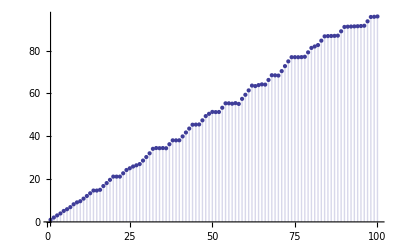

```mathematica
DiscretePlot[x-sm[x,300],{x,1,100}]
```

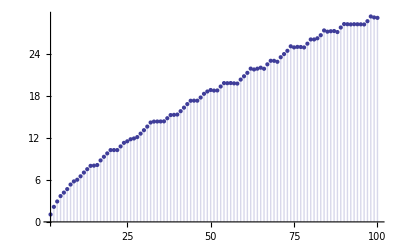

```mathematica
DiscretePlot[LogIntegral[x]-sm3[x,100],{x,2,100}]
```

```mathematica
N@vl[100,Im@ZetaZero@1]
```

1.05794

```mathematica
Re[2 x^(A+f I)/(A+f I)]/.x->100./.A->-.5/.f->Im@ZetaZero@1
```

0.0112159

```mathematica
sm2[100,1]
```

1.05794+0. ⅈ

```mathematica
x^N[ZetaZero[j]]/N[ZetaZero[j]]/.x->100./.j->1
```

0.528969+0.469138 ⅈ

```mathematica
ExpIntegralEi[10.+I]
```

1568.28+1914.17 ⅈ

```mathematica
be[x_,t_]:=EulerGamma+Log[Abs[x]]+Sum[x^k/k/k!,{k,1,t}]
bea[x_,t_]:=Table[x^k/k/k!,{k,1,t}]
```

```mathematica
be[10.+14I,20]
```

38682.-95730.4 ⅈ

```mathematica
N@LogIntegral[100^ZetaZero[1]]
```

1.35421+6.31436 ⅈ

```mathematica
N@ExpIntegralEi[ZetaZero[1]Log[100.]]
```

0.116437+3.24171 ⅈ

```mathematica
Log[100.]
```

4.60517

```mathematica
be[ZetaZero[1]Log[100.],10]
```

-3.25919×10^10+1.88372×10^10 ⅈ

```mathematica
N@ExpIntegralEi[ZetaZero[1]Log[100.]]
```

0.116437+3.24171 ⅈ

```mathematica
(D[LaguerreL[-z,ZetaZero[1]Log[100.]],z]/.z->0 )+Log[ZetaZero[1]Log[100.]]+EulerGamma
```

0.116437+3.24171 ⅈ

```mathematica
N@LogIntegral[100^ZetaZero[1]]
```

1.35421+6.31436 ⅈ

```mathematica
br[x_,t_]:=Sum[(-1)^(k+1)/k (-1)^k GammaRegularized[k,0,-Log[x]],{k,1,t}]
```

```mathematica
br[100.,50]
```

28.0217-2.09386×10^-14 ⅈ

```mathematica
FullSimplify[((A^2+(f I)^2))^(1/2)]
```

√(A^2-f^2)

```mathematica
be[x_,t_]:=EulerGamma+Log[Abs[x]]+Sum[x^k/k/k!,{k,1,t}]
be2[A_,f_,t_]:=EulerGamma+Log[Abs[A+ f I]]+Sum[(A+f I)^k/k/k!,{k,1,t}]
be2a[A_,f_,t_]:=ExpIntegralEi[A+f I]
be3[A_,f_,t_]:=EulerGamma+(1/2)Log[A^2+f^2]+Sum[(A+f I)^k/k/k!,{k,1,t}]
be4[A_,f_,t_]:=EulerGamma+(1/2)Log[A^2+f^2]+Sum[Sum[Binomial[k,2j](-1)^j A^(k-2j) f^(2j),{j,0,Floor[k/2]}]/k/k!,{k,1,t}]
be4b[A_,f_,t_]:=Sum[Sum[Binomial[k,2j](-1)^j A^(k-2j) f^(2j),{j,0,Floor[k/2]}]/k/k!,{k,1,t}]
be4a[A_,f_,t_]:=I Sum[Sum[Binomial[k,2j+1](-1)^j A^(k-2j-1) f^(2j+1),{j,0,Floor[k/2]}]/k/k!,{k,1,t}]
sm3[x_,t_]:=N@Table[Re[ExpIntegralEi[ZetaZero[j]Log[x]]+ExpIntegralEi[ZetaZero[-j]Log[x]]],{j,1,t}]
sm4[x_,t_,t2_]:=N[2Table[be4[Re[ZetaZero[j]]Log[x],Im[ZetaZero[j]]Log[x],t2],{j,1,t}]]
```

```mathematica
N@be4[.5 Log[10.],Im@ZetaZero@1Log[10.],101.]
```

0.0885639

```mathematica
N@be[(.5+Im@ZetaZero@1I)Log[10],100.]
```

0.088171+1.56513 ⅈ

```mathematica
N@be[10+I,100.]
```

1568.28+1914.07 ⅈ

```mathematica
Expand[(A+f I)^5]
```

A^5+5 ⅈ A^4 f-10 A^3 f^2-10 ⅈ A^2 f^3+5 A f^4+ⅈ f^5

```mathematica
FullSimplify[Sum[Binomial[k,j]A^(k-j) I^j f^j,{j,0,k}]]
```

A^k (1+(ⅈ f)/A)^k

```mathematica
Sum[Binomial[k,2j](-1)^j A^(k-2j) f^(2j),{j,0,Floor[k/2]}]
```

A^5-10 A^3 f^2+5 A f^4

```mathematica
sm3[3,10]
```

{0.045795,-0.132346,0.0914722,0.0943251,-0.0955739,-0.0357901,0.0631589,-0.0327046,0.041109,-0.0604237}

```mathematica
sm4[3,10,2000]
```

{0.045795,-0.132346,0.0914682,0.0933917,-0.094645,-1.19346,-74.6775,-445.621,-149764.,109505.}

```mathematica
N@Sum[be4[Re[ZetaZero[j]]Log[10.],Im[ZetaZero[j]]Log[10.],150],{j,1,1}]
```

0.0885639

```mathematica
ExpIntegralEi[ZetaZero[1]Log[10.]]
```

0.0880046+3.10063 ⅈ

```mathematica
2N@be[ZetaZero[1]Log[10],2000]
```

0.176055+3.13088 ⅈ

```mathematica
1/(1-2^(1-s))/.s->.3+4I
```

0.377123-0.0878555 ⅈ

```mathematica
1/(1-2^(1-A-f I))/.A->.3/.f->4
```

0.377123-0.0878555 ⅈ

```mathematica
1/(1-2^(1-A)2^(-f I))/.A->.3/.f->4
```

0.377123-0.0878555 ⅈ

```mathematica
1/(1-2^(1-A)E^(-f Log[2] I ))/.A->.3/.f->4
```

0.377123-0.0878555 ⅈ

```mathematica
1/(1-2^(1-A)(Cos[-f Log[2]]+I Sin[-f Log[2]]))/.A->.3/.f->4
```

0.377123-0.0878555 ⅈ

```mathematica
1/(1-2^(1-A)Cos[-f Log[2]]-I 2^(1-A) Sin[-f Log[2]])/.A->.3/.f->4
```

0.377123-0.0878555 ⅈ

```mathematica
(1-2^(1-A)Cos[-f Log[2]]+I 2^(1-A) Sin[-f Log[2]])/((1-2^(1-A)Cos[-f Log[2]])^2+ (2^(1-A) Sin[-f Log[2]])^2)/.A->.3/.f->4
```

0.377123-0.0878555 ⅈ

```mathematica
(1-2^(1-A)Cos[-f Log[2]]+I 2^(1-A) Sin[-f Log[2]])/((1-2^(1-A)Cos[-f Log[2]])^2+ (2^(1-A) Sin[-f Log[2]])^2)
```

(1-2^(1-A) Cos[f Log[2]]-ⅈ 2^(1-A) Sin[f Log[2]])/((1-2^(1-A) Cos[f Log[2]])^2+2^(2-2 A) Sin[f Log[2]]^2)

```mathematica
FullSimplify[((1-2^(1-A)Cos[-f Log[2]])^2+ (2^(1-A) Sin[-f Log[2]])^2)]
```

4^-A (4+4^A-2^(2+A) Cos[f Log[2]])

```mathematica
(1-2^(1-A)Cos[-f Log[2]])/(4^-A (4+4^A-2^(2+A) Cos[f Log[2]]))+I (2^(1-A) Sin[-f Log[2]])/(4^-A (4+4^A-2^(2+A) Cos[f Log[2]]))/.A->.3/.f->4
```

0.377123-0.0878555 ⅈ

```mathematica
(1-2^(1-A)Cos[-f Log[2]])/(4^-A (4+4^A-2^(2+A) Cos[f Log[2]]))+I (2^(1-A) Sin[-f Log[2]])/(4^-A (4+4^A-2^(2+A) Cos[f Log[2]]))
```

```mathematica
1/(1-2^(1-s))Sum[(-1)^(j+1)/j^s,{j,1,Infinity}]/.s->.3+4I
```

0.575756+0.10773 ⅈ

```mathematica
Zeta[.3+4I]
```

0.575756+0.10773 ⅈ

```mathematica
1/(1-2^(1-(A+f I)))Sum[(-1)^(j+1)/j^(A+f I),{j,1,Infinity}]/.A->.3/.f->400
```

-1.74573+1.07588 ⅈ

```mathematica
((1-2^(1-A)Cos[-f Log[2]])/(4^-A (4+4^A-2^(2+A) Cos[f Log[2]]))+I (2^(1-A) Sin[-f Log[2]])/(4^-A (4+4^A-2^(2+A) Cos[f Log[2]])))Sum[(-1)^(j+1)/j^(A+f I),{j,1,Infinity}]/.A->.3/.f->1000
```

-0.920724+2.21155 ⅈ

```mathematica
((1-2^(1-A)Cos[-f Log[2]])/(4^-A (4+4^A-2^(2+A) Cos[f Log[2]]))+I (2^(1-A) Sin[-f Log[2]])/(4^-A (4+4^A-2^(2+A) Cos[f Log[2]])))Sum[(-1)^(j+1)/j^(A+f I),{j,1,2000}]/.A->.3/.f->1000
```

-0.937577+2.19497 ⅈ

```mathematica
FullSimplify[D[Cos[100 Log[x]],x]]
```

-(100 Sin[100 Log[x]])/x

```mathematica
FullSimplify[Sum[1/n Cos[n],{n,1,Infinity}]]
```

-1/2 Log[2-2 Cos[1]]

```mathematica
Integrate[1/n Cos[n],{n,1,Infinity}]
```

-CosIntegral[1]

```mathematica
FullSimplify[Cos[100 t]+I Sin[100 t]]
```

ⅇ^(100 ⅈ t)

```mathematica
FullSimplify@Sum[E^(-s t),{t,1,Infinity}]
```

1/(-1+ⅇ^s)

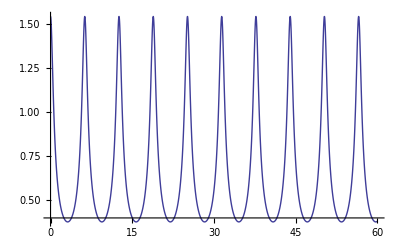

```mathematica
Plot[Abs[1/(-1+ⅇ^(.5+t I))],{t,0,60}]
```

```mathematica
Integrate[E^(-s t),{t,0,x}]/.s->.3+5I/.x->12.
```

0.0106084-0.204568 ⅈ

```mathematica
(1/(A+f I))
```

1/(A+ⅈ f)

```mathematica
(A-f I)/(A^2-f^2)
```

(A-ⅈ f)/(A^2-f^2)

```mathematica
A/(A^2-f^2)-I(f)/(A^2-f^2)
```

A/(A^2-f^2)-(ⅈ f)/(A^2-f^2)

```mathematica
Plot[(1-ⅇ^(-s x))/s,{t,0,30}]
```

```mathematica
(1-ⅇ^(-s x))/s/.s->.3+5I/.x->12.
```

0.0106084-0.204568 ⅈ

```mathematica
(1-ⅇ^(-(A+f I) x))/(A+f I)/.A->.3/.f->5/.x->12.
```

0.0106084-0.204568 ⅈ

```mathematica
(1-ⅇ^(-A x)E^(-f x I))/(A+f I)/.A->.3/.f->5/.x->12.
```

0.0106084-0.204568 ⅈ

```mathematica
((A-f I)(1-ⅇ^(-A x)E^(-f x I)))/(A^2+f^2)/.A->.3/.f->5/.x->12.
```

0.0106084-0.204568 ⅈ

```mathematica
((A-f I)(1-ⅇ^(-A x)(Cos[-f x ]+I Sin[-f x])))/(A^2+f^2)/.A->.3/.f->5/.x->12.
```

0.0106084-0.204568 ⅈ

```mathematica
((A-f I)(1-ⅇ^(-A x)Cos[-f x ]-I ⅇ^(-A x) Sin[-f x]))/(A^2+f^2)/.A->.3/.f->5/.x->12.
```

0.0106084-0.204568 ⅈ

```mathematica
((A-f I)-(A-f I)ⅇ^(-A x)Cos[-f x ]-I (A-f I)ⅇ^(-A x) Sin[-f x])/(A^2+f^2)/.A->.3/.f->5/.x->12.
```

0.0106084-0.204568 ⅈ

```mathematica
(A-A ⅇ^(-A x)Cos[-f x ]-f ⅇ^(-A x) Sin[-f x])/(A^2+f^2)+I(-f+f ⅇ^(-A x)Cos[-f x ]-A ⅇ^(-A x) Sin[-f x])/(A^2+f^2)/.A->.3/.f->5/.x->12.
```

0.0106084-0.204568 ⅈ

```mathematica
(A-ⅇ^(-A x)(A Cos[-f x ]+f  Sin[-f x]))/(A^2+f^2)-I(f+ⅇ^(-A x)(A Sin[-f x]-f Cos[-f x ]))/(A^2+f^2)/.A->.3/.f->5/.x->12.
```

0.0106084-0.204568 ⅈ

```mathematica
(A-ⅇ^(-A x)(A Cos[f x ]+f  Sin[-f x]))/(A^2+f^2)-I(f-ⅇ^(-A x)(A Sin[f x]+f Cos[f x ]))/(A^2+f^2)/.A->.3/.f->5/.x->12.
```

0.0106084-0.204568 ⅈ

```mathematica
(A-ⅇ^(-A x)(A Cos[f x ]+f  Sin[-f x]))/(A^2+f^2)/.A->0
```

Sin[f x]/f

```mathematica
(f-ⅇ^(-A x)(A Sin[f x]+f Cos[f x ]))/(A^2+f^2)/.A->0
```

(f-f Cos[f x])/f^2

```mathematica
1/(-1+ⅇ^(A+f I))/.A->.3/.f->5/.x->12.
```

-0.300099+0.629483 ⅈ

```mathematica
1/(-1+E^A ⅇ^(f I))/.A->.3/.f->5/.x->12.
```

-0.300099+0.629483 ⅈ

```mathematica
1/(-1+E^A (Cos[f]+I Sin[f]))/.A->.3/.f->5/.x->12.
```

-0.300099+0.629483 ⅈ

```mathematica
1/(-1+E^A Cos[f]+I E^A Sin[f])/.A->.3/.f->5/.x->12.
```

-0.300099+0.629483 ⅈ

```mathematica
(-1+E^A Cos[f]-I E^A Sin[f])/((-1+E^A Cos[f])^2+( E^A Sin[f])^2)/.A->.3/.f->5/.x->12.
```

-0.300099+0.629483 ⅈ

```mathematica
(-1+E^A Cos[f]-I E^A Sin[f])/((-1+E^A Cos[f])^2+( E^A Sin[f])^2)/.A->.3/.f->5/.x->12.
```

```mathematica
(-1+E^A Cos[f])/((-1+E^A Cos[f])^2+( E^A Sin[f])^2)/.A->.3/.f->5/.x->12.
```

-0.300099

```mathematica
(-1+E^A Cos[f])/((-1+E^A Cos[f])^2+( E^A Sin[f])^2)
```

```mathematica
FullSimplify[(-1+E^A Cos[f])^2+( E^A Sin[f])^2]
```

1+ⅇ^(2 A)-2 ⅇ^A Cos[f]

```mathematica
FullSimplify[(-1+E^A Cos[f])/(1+ⅇ^(2 A)-2 ⅇ^A Cos[f])]
```

(-1+ⅇ^A Cos[f])/(1+ⅇ^(2 A)-2 ⅇ^A Cos[f])

```mathematica
N@Zeta[10I]
```

```mathematica
1.756468592974971-0.1015119854361739 ⅈ
```

1.75647-0.101512 ⅈ

```mathematica
N@Zeta[1000I]
```

-8.46309098852087+8.34334485626739 ⅈ

```mathematica
-10.4-2.7
```

-13.1

```mathematica
N@Zeta[10000 I]
```

```mathematica
530*3
```

1590

```mathematica
6.517210426253009+0.18128842533808529 ⅈ
```

6.51721+0.181288 ⅈ

```mathematica
bk[s_,t_]:=Sum[s^k,{k,0,t}]
bk2[s_,t_]:=Sum[k^s,{k,1,t}]
```

```mathematica
Zeta[.02I]
```

```mathematica
-0.4995988886255318-0.018370767581264345 ⅈ
```

```mathematica
-0.4614111392162328-0.1760891180160563 ⅈ
```

-0.461411-0.176089 ⅈ

```mathematica
0.31472576404209895-0.23167964875052027 ⅈ
```

```mathematica
Zeta[-.5]
```

-0.207886

```mathematica
Expand[(1-x/2)(1-x/3)(1-x/4 )(1-x/5)]
```

1-(77 x)/60+(71 x^2)/120-(7 x^3)/60+x^4/120

```mathematica
Log[1-14 x+71 x^2-154 x^3+120 x^4]
```

Log[1-14 x+71 x^2-154 x^3+120 x^4]

```mathematica
Log[(1-2x)(1-3x)(1-4x )(1-5x)]
```

```mathematica
N@Log[(1-x/5) (1-x/4) (1-x/3) (1-x/2)]/.x->1
```

-1.60944

```mathematica
N@Sum[Log[1-1/k],{k,2,5}]
```

-1.60944

```mathematica
Sum[1/k x^k,{k,1,Infinity}]
```

-Log[1-x]

```mathematica
D[1-(77 x)/60+(71 x^2)/120-(7 x^3)/60+x^4/120,x]/.x->0
```

-77/60

```mathematica
Sum[-1/k,{k,2,5}]
```

-77/60

```mathematica
Product[1-s/r,{r,ZetaZero}]
```

Pochhammer[1-s,ZetaZero]/(ZetaZero!)

```mathematica
pe[x_,t_]:=EulerGamma+Log@Log@x+x^(1/2)Sum[(-1)^(n-1)(Log@x)^n/n!/2^(n-1)  1/(2k+1),{n,1,t},{k,0,Floor[(n-1)/2]}]
```

```mathematica
pe[1000.,15]
```

177.612

```mathematica
LogIntegral[1000.]
```

177.61

```mathematica
Table[ j!,{j,0,20}]
```

{1,1,2,6,24,120,720,5040,40320,362880,3628800,39916800,479001600,6227020800,87178291200,1307674368000,20922789888000,355687428096000,6402373705728000,121645100408832000,2432902008176640000}

```mathematica
N@EulerGamma
```

```mathematica
0.5772156649015329
```

0.577216

```mathematica
Log[100.]^15
```

8.88557×10^9

```mathematica
LogIntegral[4245.25]
```

594.827

```mathematica
FullSimplify[Zeta'[s]/Zeta[s]/.s->0]
```

Log[2 π]

```mathematica
FullSimplify@Log[1-s/p]
```

Log[1-s/p]

```mathematica
rr[s_,t_]:=Pi^(s/2)/2/(s-1)/Gamma[1+s/2]Product[(1-s/ZetaZero[j])(1-s/ZetaZero[-j]),{j,1,t}]
```

```mathematica
N@rr[2+6I,1000]
```

0.951822+0.148437 ⅈ

```mathematica
N@Zeta[2+6I]
```

0.926863+0.156867 ⅈ

```mathematica
rl[s_,t_]:=Log[Pi^(s/2)/2/(s-1)/Gamma[1+s/2]Product[(1-s/ZetaZero[j])(1-s/ZetaZero[-j]),{j,1,t}]]
rla[s_,t_]:=Log[Pi^(s/2)]-Log[2]-Log[(s-1)]-Log[Gamma[1+s/2]]+Log[Product[(1-s/ZetaZero[j])(1-s/ZetaZero[-j]),{j,1,t}]]
rlb[s_,t_]:=(s/2)Log[Pi]-Log[2]-Log[s-1]-Log[Gamma[1+s/2]]+Sum[Log[(1-s/ZetaZero[-j])],{j,1,t}]+Sum[Log[(1-s/ZetaZero[j])],{j,1,t}]
rlc[s_,t_]:=(s/2)Log[Pi]-Log[2]-Log[s-1]-Log[Gamma[1+s/2]]-Sum[Sum[(s/ZetaZero[-j])^k/k,{k,1,Infinity}],{j,1,t}]-Sum[Log[(1-s/ZetaZero[j])],{j,1,t}]
```

```mathematica
N@rlb[1.6,40]
```

0.821794+0. ⅈ

```mathematica
N@Log[Zeta[1.6]]
```

0.826701

```mathematica
Expand@Log[1-s/ZetaZero[1]]
```

Log[1-s/ZetaZero[1]]

```mathematica
FullSimplify@Sum[-1/k (s/ZetaZero[1])^k,{k,1,Infinity}]
```

Log[1-s/ZetaZero[1]]

```mathematica
Clear[ms,ps,ds,dds]
D2[n_,0]:=UnitStep[n-1]
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}]
d2[n_,k_]:=d2[n,k]=D2[n,k]-D2[n-1,k]
ps[1,s_]:=0
ps[n_,s_]:=ps[n,s]=FullSimplify[MangoldtLambda[n]/Log[n]]n^-s+ps[n-1,s]
ms[1,s_]:=1
ms[n_,s_]:=ms[n,s]=MoebiusMu[n]n^-s+ms[n-1,s]
ds[1,s_]:=1
ds[n_,s_]:=ds[n,s]=n^-s+ds[n-1,s]
dds[1,s_,k_]:=0
dds[n_,s_,k_]:=dds[n,s,k]=d2[n,k]n^-s+dds[n-1,s,k]
```

```mathematica
FullSimplify@ds[10,s]
```

1+2^-s+3^-s+4^-s+5^-s+6^-s+7^-s+8^-s+9^-s+10^-s

```mathematica
DiscretePlot[Re@dds[n,100I,2],{n,1,1000}]
```

```mathematica
N@1/Zeta[100I]
```

0.153321-0.00426492 ⅈ

```mathematica
N@Log@Log@6000.
```

2.16327

```mathematica
dds[10,s,2]
```

2^(1-3 s)+2^(1-s) 3^-s+4^-s+2^(1-s) 5^-s+9^-s

```mathematica
d2[2,1]
```

1

```mathematica
DiscretePlot[Re@dds[n,100I,3],{n,1,2000}]
```

```mathematica
DiscretePlot[Re@dds[n,100I,2],{n,1,2000}]
```

```mathematica
N@Sin[100 Log[x]]/.x->1000000000000
```

-0.997454

```mathematica
N@Sin[10000 Log[x]]/.x->1000000000001
```

0.753974

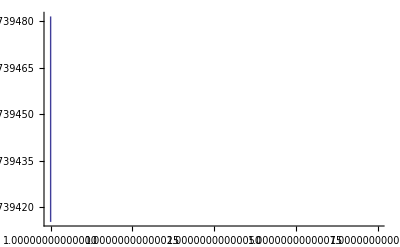

```mathematica
Plot[Sin[10000 Log[x]],{x,1000000000000,1000000000000+1}]
```

```mathematica
p1[n_,s_]:=Sum[j^-s,{j,1,n}]
p2[n_,s_]:=Integrate[j^-s,{j,0,n}]
```

```mathematica
N@p1[1000,-.3+100I]-N@p2[1000,-.3+100I]
```

16.5331+1.88315 ⅈ

```mathematica
N@Zeta[-.3+100I]
```

12.8128+0.490515 ⅈ

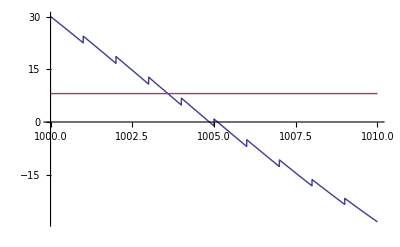

```mathematica
Plot[{Re@p1[n,-.1+100I]- Re@p2[n,-.3+100I],Re@N@Zeta[-.1+100I]},{n,1000,1010}]
```

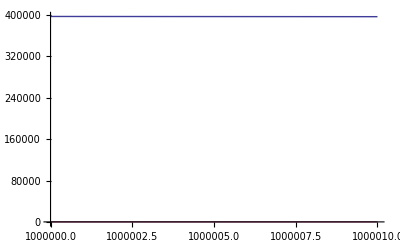

```mathematica
Plot[{Re@p1[n,-.1+100I]- Re@p2[n,-.3+100I],Re@N@Zeta[-.1+100I]},{n,1000000,1000010}]
```

```mathematica
Expand[(1-x/-2)(1-x/-1)(1-x/3)(1-x/4)]
```

1+(11 x)/12-(7 x^2)/24-x^3/6+x^4/24

```mathematica
ex[s_]:=Pi^(s/2)/(2(s-1)Gamma[1+s/2])
ex2[s_,t_]:=Product[(1-s/ZetaZero[j])(1-s/ZetaZero[-j]),{j,1,t}]
ex3[s_,t_]:=ex[s]ex2[s,t]
```

```mathematica
N@ex[10I]
```

22.2245+5.37482 ⅈ

```mathematica
N@ex2[10I,60]
```

0.112627-0.0291961 ⅈ

```mathematica
N@ex3[10I,1000]
```

1.88826-0.0955008 ⅈ

```mathematica
N@Zeta[10I]
```

1.75647-0.101512 ⅈ

```mathematica
N@ex3[10I,1000]
```

1.88826-0.0955008 ⅈ

```mathematica
N@Zeta[2I]
```

0.314726-0.23168 ⅈ

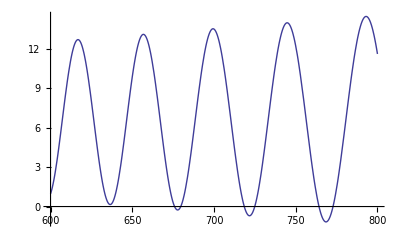

```mathematica
Plot[,{x,600,800}]
```

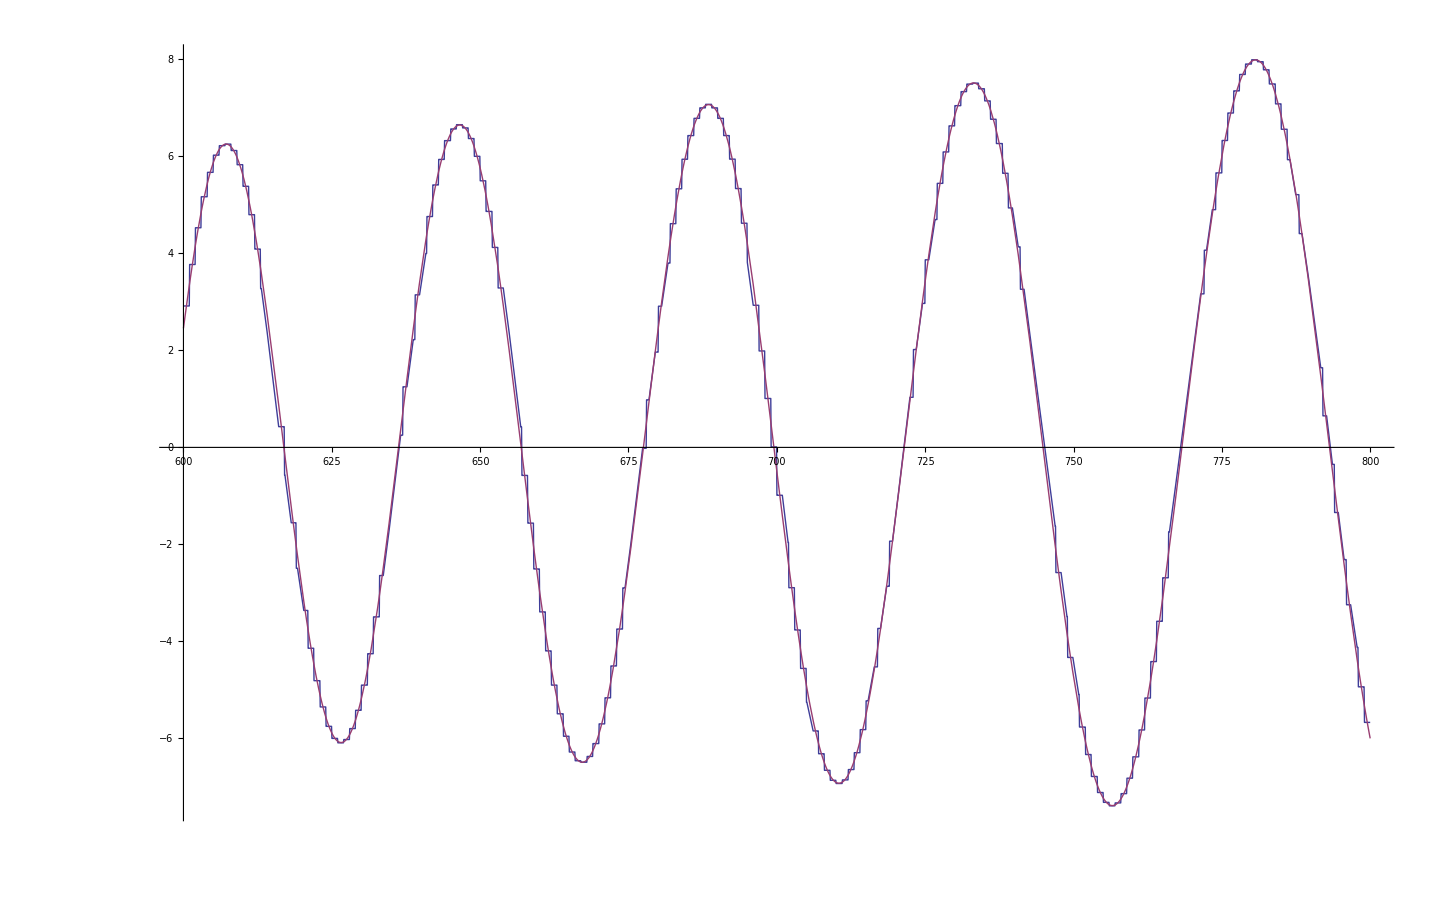

```mathematica
Plot[{ Im[Sum[j^-(100 I),{j,1,x}]],Im[Zeta[100 I]+x^(1-100I)/(1-100I)]},{x,600,800}]
```

```mathematica
N@Zeta[-1+2I]
```

0.168916-0.070516 ⅈ

```mathematica
-123.54067467712193+90.0000774946647 ⅈ
```

-123.541+90.0001 ⅈ

```mathematica
0.3563343671948756+0.9319978312333586 ⅈ
```

```mathematica
-123.54067467712193+90.0000774946647 ⅈ
```

```mathematica
14.306224558410431+27.183025808206345 ⅈ
```

```mathematica
1/12.
```

0.0833333

```mathematica
Integrate[t^(-3-1/10I),{t,0,x}]
```

(-200/401+(10 ⅈ)/401) x^(-2-ⅈ/10)

```mathematica
Sum[E^(s t),{t,0,Infinity}]
```

-1/(-1+ⅇ^s)